```mathematica
n=6;
m=Table[
Which[j==i-1,1-p,
i==1&&j<n,p,
i==1&&j==n,2p,
i==n&&j==n,1-p,
True,0],{i,1,n},{j,1,n}];
MatrixForm[m]
```

(p | p | p | p | p | 2 p
1-p | 0 | 0 | 0 | 0 | 0
0 | 1-p | 0 | 0 | 0 | 0
0 | 0 | 1-p | 0 | 0 | 0
0 | 0 | 0 | 1-p | 0 | 0
0 | 0 | 0 | 0 | 1-p | 1-p)

```mathematica
Simplify[Det[m]]
```

(-1+p)^5 p

```mathematica
Eigenvalues[m/.p->1/10]
```

{Root1.05Root[-59049-1000000 #1^5+1000000 #1^6&,2]1.0469453415487666,Root0.443+0.419 ⅈRoot[-59049-1000000 #1^5+1000000 #1^6&,6]0.44349707733150445,Root0.443-0.419 ⅈRoot[-59049-1000000 #1^5+1000000 #1^6&,5]0.44349707733150445,Root-0.206+0.498 ⅈRoot[-59049-1000000 #1^5+1000000 #1^6&,4]-0.20591964739731822,Root-0.206-0.498 ⅈRoot[-59049-1000000 #1^5+1000000 #1^6&,3]-0.20591964739731822,Root-0.522Root[-59049-1000000 #1^5+1000000 #1^6&,1]-0.5221002014171391}

```mathematica
Eigenvalues[m/.p->1/10][[1]]//N
```

1.04695

```mathematica
Eigenvectors[m/.p->1/10]
```

{{Root0.299Root[-2+4 #1-19 #1^2-172 #1^3-1400 #1^4-10000 #1^5+59049 #1^6&,2]0.298978053947882,Root0.257Root[2-4 #1+23 #1^2-162 #1^3-117 #1^4-1000 #1^5+6561 #1^6&,1]0.2570146099079425,Root0.221Root[-2+4 #1+27 #1^2+32 #1^3-243 #1^4-100 #1^5+729 #1^6&,2]0.22094099829028532,Root0.190Root[2-4 #1-31 #1^2-18 #1^3-10 #1^5+81 #1^6&,1]0.1899305441935476,Root0.163Root[-2+4 #1+35 #1^2+80 #1^3+85 #1^4+44 #1^5+9 #1^6&,2]0.16327260172085173,1},{Root0.0957-0.110 ⅈRoot[-2+4 #1-19 #1^2-172 #1^3-1400 #1^4-10000 #1^5+59049 #1^6&,5]0.0956677947072281,Root-8.90 × 10^-3-0.215 ⅈRoot[2-4 #1+23 #1^2-162 #1^3-117 #1^4-1000 #1^5+6561 #1^6&,5]-0.008896387864908976,Root-0.227-0.221 ⅈRoot[-2+4 #1+27 #1^2+32 #1^3-243 #1^4-100 #1^5+729 #1^6&,3]-0.2270405824558716,Root-0.467-6.73 × 10^-3 ⅈRoot[2-4 #1-31 #1^2-18 #1^3-10 #1^5+81 #1^6&,3]-0.467107636422471,Root-0.507+0.466 ⅈRoot[-2+4 #1+35 #1^2+80 #1^3+85 #1^4+44 #1^5+9 #1^6&,6]-0.5072254696316617,1},{Root0.0957+0.110 ⅈRoot[-2+4 #1-19 #1^2-172 #1^3-1400 #1^4-10000 #1^5+59049 #1^6&,6]0.0956677947072281,Root-8.90 × 10^-3+0.215 ⅈRoot[2-4 #1+23 #1^2-162 #1^3-117 #1^4-1000 #1^5+6561 #1^6&,6]-0.008896387864908976,Root-0.227+0.221 ⅈRoot[-2+4 #1+27 #1^2+32 #1^3-243 #1^4-100 #1^5+729 #1^6&,4]-0.2270405824558716,Root-0.467+6.73 × 10^-3 ⅈRoot[2-4 #1-31 #1^2-18 #1^3-10 #1^5+81 #1^6&,4]-0.467107636422471,Root-0.507-0.466 ⅈRoot[-2+4 #1+35 #1^2+80 #1^3+85 #1^4+44 #1^5+9 #1^6&,5]-0.5072254696316617,1},{Root-0.0710-0.157 ⅈRoot[-2+4 #1-19 #1^2-172 #1^3-1400 #1^4-10000 #1^5+59049 #1^6&,3]-0.07100609605395877,Root-0.198+0.210 ⅈRoot[2-4 #1+23 #1^2-162 #1^3-117 #1^4-1000 #1^5+6561 #1^6&,4]-0.19764115039462424,Root0.451+0.171 ⅈRoot[-2+4 #1+27 #1^2+32 #1^3-243 #1^4-100 #1^5+729 #1^6&,6]0.4510339597584876,Root-0.0244-0.806 ⅈRoot[2-4 #1-31 #1^2-18 #1^3-10 #1^5+81 #1^6&,5]-0.0244494885108722,Root-1.23+0.553 ⅈRoot[-2+4 #1+35 #1^2+80 #1^3+85 #1^4+44 #1^5+9 #1^6&,4]-1.2287996082192425,1},{Root-0.0710+0.157 ⅈRoot[-2+4 #1-19 #1^2-172 #1^3-1400 #1^4-10000 #1^5+59049 #1^6&,4]-0.07100609605395877,Root-0.198-0.210 ⅈRoot[2-4 #1+23 #1^2-162 #1^3-117 #1^4-1000 #1^5+6561 #1^6&,3]-0.19764115039462424,Root0.451-0.171 ⅈRoot[-2+4 #1+27 #1^2+32 #1^3-243 #1^4-100 #1^5+729 #1^6&,5]0.4510339597584876,Root-0.0244+0.806 ⅈRoot[2-4 #1-31 #1^2-18 #1^3-10 #1^5+81 #1^6&,6]-0.0244494885108722,Root-1.23-0.553 ⅈRoot[-2+4 #1+35 #1^2+80 #1^3+85 #1^4+44 #1^5+9 #1^6&,3]-1.2287996082192425,1},{Root-0.179Root[-2+4 #1-19 #1^2-172 #1^3-1400 #1^4-10000 #1^5+59049 #1^6&,1]-0.1789505731701178,Root0.308Root[2-4 #1+23 #1^2-162 #1^3-117 #1^4-1000 #1^5+6561 #1^6&,2]0.30847625688699654,Root-0.532Root[-2+4 #1+27 #1^2+32 #1^3-243 #1^4-100 #1^5+729 #1^6&,1]-0.531753541647232,Root0.917Root[2-4 #1-31 #1^2-18 #1^3-10 #1^5+81 #1^6&,2]0.9166404957965956,Root-1.58Root[-2+4 #1+35 #1^2+80 #1^3+85 #1^4+44 #1^5+9 #1^6&,1]-1.5801113349079323,1}}

```mathematica
{1,1,1,1,1}.m.{1,0,0,0,0}
```

1

```mathematica
{1,1,1,1,1}.m.m.{1,0,0,0,0}
```

1

```mathematica
{1,1,1,1,1}.m.m.m.{1,0,0,0,0}
```

1

```mathematica
{1,1,1,1,1}.m.m.m.m.{1,0,0,0,0}
```

1

```mathematica
Simplify[{1,1,1,1,1,1}.m.m.m.m.m.{1,0,0,0,0,0}]
```

1

```mathematica
Simplify[{1,1,1,1,1,1}.MatrixPower[m,5].{1,0,0,0,0,0}]
```

1

```mathematica
Simplify[{1,1,1,1,1,1}.MatrixPower[m,6].{1,0,0,0,0,0}]
```

1+p-5 p^2+10 p^3-10 p^4+5 p^5-p^6

```mathematica
Simplify[{1,1,1,1,1,1}.MatrixPower[m,20].{1,0,0,0,0,0}]
```

1+15 p-30 p^2-290 p^3+1725 p^4-4275 p^5+4885 p^6+2310 p^7-20580 p^8+44650 p^9-62325 p^10+63900 p^11-50005 p^12+30030 p^13-13650 p^14+4550 p^15-1050 p^16+150 p^17-10 p^18

```mathematica
Simplify[{1,1,1,1,1,1}.MatrixPower[m,20].{1,0,0,0,0,0}]+O[p]^2
```

1+15 p+O[p]^2

```mathematica
Simplify[{1,1,1,1,1,1}.MatrixPower[m,101].{1,0,0,0,0,0}]+O[p]^2
```

1+96 p+O[p]^2

```mathematica
Exp[0.1]
```

1.10517

```mathematica
Simplify[{1,1,1,1,1,1}.MatrixPower[m,20].{1,0,0,0,0,0}]/.p->1
```

1

```mathematica
Simplify[{1,1,1,1,1,1}.MatrixPower[m,20].{1,0,0,0,0,0}]/.p->2
```

71

```mathematica
Simplify[{1,1,1,1,1}.m.m.m.m.m.m.m.{1,0,0,0,0}]
```

1+3 p-12 p^2+18 p^3-12 p^4+3 p^5

```mathematica
Simplify[{1,1,1,1,1,1}.MatrixPower[m,7].{1,0,0,0,0,0}]
```

1+2 p-10 p^2+20 p^3-20 p^4+10 p^5-2 p^6

```mathematica
Simplify[{1,1,1,1,1}.m.m.m.m.m.m.m.m.{1,0,0,0,0}]
```

1+4 p-16 p^2+24 p^3-16 p^4+4 p^5

```mathematica
Simplify[{1,1,1,1,1}.m.m.m.m.m.m.m.m.m.{1,0,0,0,0}]
```

1+5 p-20 p^2+30 p^3-20 p^4+5 p^5

```mathematica
Simplify[{1,1,1,1,1}.m.m.m.m.m.m.m.m.m.m.{1,0,0,0,0}]
```

1+6 p-23 p^2+28 p^3+4 p^4-50 p^5+70 p^6-56 p^7+28 p^8-8 p^9+p^10

```mathematica
Simplify[{1,1,1,1,1}.MatrixPower[m,10].{1,0,0,0,0}]
```

1+6 p-23 p^2+28 p^3+4 p^4-50 p^5+70 p^6-56 p^7+28 p^8-8 p^9+p^10

```mathematica
Simplify[{1,1,1,1,1}.MatrixPower[m,20].{1,0,0,0,0}]
```

1+16 p+2 p^2-376 p^3+1113 p^4-7580 p^6+23464 p^7-40684 p^8+46848 p^9-36278 p^10+16280 p^11+550 p^12-7744 p^13+7336 p^14-4312 p^15+1820 p^16-560 p^17+120 p^18-16 p^19+p^20

```mathematica
Simplify[{1,1,1,1,1}.MatrixPower[m,100].{1,0,0,0,0}]
```

1+96 p+3802 p^2+76824 p^3+729493 p^4+176256 p^5-54490160 p^6-232577472 p^7+2503045372 p^8+13494185216 p^9-109844574584 p^10-401145482400 p^11+4448160912380 p^12+2280706502784 p^13-130377257245136 p^14+343696038623936 p^15+1851648796063450 p^16-13934671768105920 p^17+17240984428060340 p^18+178057982927432112 p^19-1001376414598749134 p^20+1495485263208705920 p^21+7395412310398808560 p^22-49881291477295268160 p^23+125340317822127557180 p^24-1216592823151369265630 p^26+5026963249200310334320 p^27-10528048990155441077720 p^28+4410408933556210876720 p^29+55354738376032532559980 p^30-241235149947085394154800 p^31+585864992247537035346196 p^32-861691259864242105439376 p^33+205768173495098880840172 p^34+3167561087820177388301272 p^35-11547531381856945515001995 p^36+25789398000394346416486720 p^37-41564050497576587673765104 p^38+45066465210045076544183136 p^39-11573056005103414173013256 p^40-88720294224440419945206720 p^41+275211661829075571793641070 p^42-535204027468629779620023360 p^43+806632716797849440871242042 p^44-979249213063966987742160544 p^45+923239173375761672803289860 p^46-540631351992155585993765120 p^47-180783901405545529196458620 p^48+1138765255949046901677968800 p^49-2133142334530348922578154798 p^50+2926600686478553365854126560 p^51-3325817462728028352343975730 p^52+3247578406777023546584889280 p^53-2741560300845009836745028280 p^54+1962831396221607487516796800 p^55-1110379293872650008551153600 p^56+360675936474146624480056320 p^57+177591295137459977171596660 p^58-475733999668359479758795280 p^59+568570624184705752785939050 p^60-523612491961889748686500400 p^61+411259390990675566357371200 p^62-285626676257473772819336624 p^63+178085276640201427369041136 p^64-100177120222423824400497296 p^65+50717476500726549813912520 p^66-22849914299768420902148960 p^67+8910058976720862503649810 p^68-2794775721117264237794496 p^69+523131604596382621630752 p^70+120397831678939640171200 p^71-196249802325092319137120 p^72+133499802833831820660160 p^73-69625768640700853437800 p^74+30967808120683714934848 p^75-12200251790402899757240 p^76+4330624979952965173120 p^77-1396507500089175556160 p^78+410620113651524566240 p^79-110173716156868526690 p^80+26935660270846228000 p^81-5979136076945572970 p^82+1197743866617671320 p^83-214418701379307275 p^84+33751722247439440 p^85-4533750437039300 p^86+485531526100600 p^87-32641608468140 p^88-1186442502560 p^89+861250633870 p^90-177368727800 p^91+25999505950 p^92-3055580000 p^93+297269896 p^94-23997512 p^95+1581580 p^96-82160 p^97+3160 p^98-80 p^99+p^100

```mathematica
Simplify[{1,1,1,1,1}.m.m.m.m.m.m.m.m.m.{1,0,0,0,0}]
```

1+5 p-20 p^2+30 p^3-20 p^4+5 p^5

```mathematica
Factor[%]
```

1+5 p-20 p^2+30 p^3-20 p^4+5 p^5

```mathematica
Eigenvalues[m]
```

{Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,1],Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,2],Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,3],Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,4],Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,5]}

```mathematica
Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,1]/.p->1/10//N
```

1.0533

```mathematica
Eigenvectors[m]
```

{{(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,1]^3 (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,1]))/(-1+p)^4,-(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,1]^2 (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,1]))/(-1+p)^3,(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,1] (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,1]))/(-1+p)^2,-(-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,1])/(-1+p),1},{(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,2]^3 (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,2]))/(-1+p)^4,-(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,2]^2 (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,2]))/(-1+p)^3,(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,2] (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,2]))/(-1+p)^2,-(-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,2])/(-1+p),1},{(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,3]^3 (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,3]))/(-1+p)^4,-(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,3]^2 (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,3]))/(-1+p)^3,(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,3] (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,3]))/(-1+p)^2,-(-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,3])/(-1+p),1},{(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,4]^3 (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,4]))/(-1+p)^4,-(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,4]^2 (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,4]))/(-1+p)^3,(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,4] (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,4]))/(-1+p)^2,-(-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,4])/(-1+p),1},{(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,5]^3 (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,5]))/(-1+p)^4,-(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,5]^2 (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,5]))/(-1+p)^3,(Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,5] (-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,5]))/(-1+p)^2,-(-1+p+Root[-p+4 p^2-6 p^3+4 p^4-p^5-#1^4+#1^5&,5])/(-1+p),1}}

```mathematica
Eigenvalues[m]
```

{Root[-p+5 p^2-10 p^3+10 p^4-5 p^5+p^6-#1^5+#1^6&,1],Root[-p+5 p^2-10 p^3+10 p^4-5 p^5+p^6-#1^5+#1^6&,2],Root[-p+5 p^2-10 p^3+10 p^4-5 p^5+p^6-#1^5+#1^6&,3],Root[-p+5 p^2-10 p^3+10 p^4-5 p^5+p^6-#1^5+#1^6&,4],Root[-p+5 p^2-10 p^3+10 p^4-5 p^5+p^6-#1^5+#1^6&,5],Root[-p+5 p^2-10 p^3+10 p^4-5 p^5+p^6-#1^5+#1^6&,6]}

```mathematica
%/.p->1/10//N
```

{-0.5221,1.04695,-0.20592-0.497529 ⅈ,-0.20592+0.497529 ⅈ,0.443497-0.419404 ⅈ,0.443497+0.419404 ⅈ}

```mathematica
Expand[(1-p)^5 p]
```

p-5 p^2+10 p^3-10 p^4+5 p^5-p^6

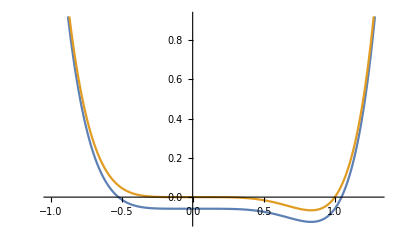

```mathematica
Plot[{((-p+5 p^2-10 p^3+10 p^4-5 p^5+p^6)/.p->1/10)-#1^5+#1^6&@x,x^6-x^5},{x,-1,1.3}]
```